1+(4 DW (-1+S) Δ^2)/(2 s0+4 Δ^2)

(Dark √(2+(4 DW (-1+S) Δ^2)/(2 s0+4 Δ^2)))/(B s0)

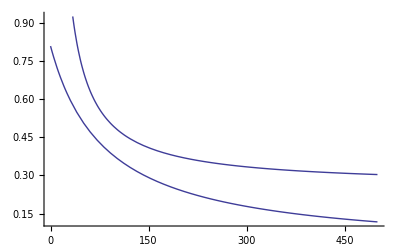

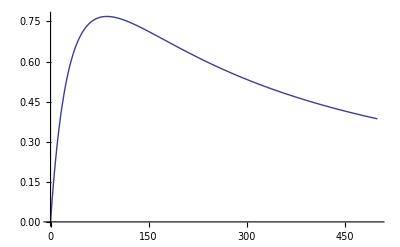

```mathematica
It = (DW 4 Δ^2)/(4 Δ^2+2 s0)(S-1) +1 
dIt= Dark/(s0 B)√(1+It)
dIdS=(DW 4 Δ^2)/(4 Δ^2+2 s0);

Plot[{dIdS, dIt/(It-1)}/.{Dark->500, B->200,Δ->6.5,DW->0.81,S->1.2},{s0,0,500}]
Plot[{ dIdS/(dIt/(It-1))}/.{Dark->500, B->200,Δ->6.5,DW->0.81,S->1.2},{s0,0,500}]
```

```mathematica
dS =  ((DW 4 Δ^2)/(4 Δ^2+2 s0))^-1 dIt
```

(Dark (2 s0+4 Δ^2) √(2+(4 DW (-1+S) Δ^2)/(2 s0+4 Δ^2)))/(4 DW Itof Δ^2)

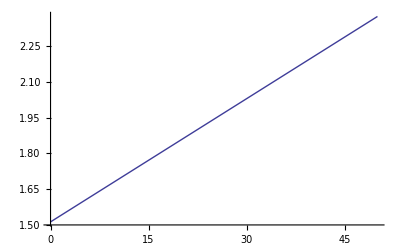

```mathematica
Plot[dS/(S-1)/.{Dark->500, Itof->3000,Δ->6.5,DW->0.81,S->1.2},{s0,0,50}]
```